This code shows how to use a place holder to plot gaps in a ListLinePlot

### Using the Placeholder[] function:

```mathematica
mylist=Table[If[i<5||i==10,5,Placeholder[]],{i,1,10,1}]
```

{5,5,5,5,□,□,□,□,□,5}

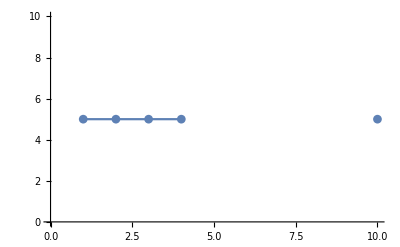

```mathematica
ListPlot[mylist,Joined->True,PlotMarkers->Automatic]
```